```mathematica
(*シミュレーション用のプログラムに食わせるグラフデータを出力する*)
```

Nagent=10

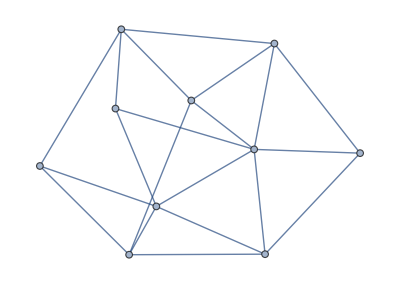

dmax=6

Perron matrix=(2/7 | 1/7 | 0 | 1/7 | 0 | 0 | 0 | 1/7 | 1/7 | 1/7
1/7 | 3/7 | 1/7 | 1/7 | 0 | 0 | 0 | 0 | 0 | 1/7
0 | 1/7 | 4/7 | 1/7 | 1/7 | 0 | 0 | 0 | 0 | 0
1/7 | 1/7 | 1/7 | 1/7 | 1/7 | 1/7 | 0 | 0 | 1/7 | 0
0 | 0 | 1/7 | 1/7 | 3/7 | 1/7 | 1/7 | 0 | 0 | 0
0 | 0 | 0 | 1/7 | 1/7 | 3/7 | 1/7 | 0 | 0 | 1/7
0 | 0 | 0 | 0 | 1/7 | 1/7 | 3/7 | 1/7 | 1/7 | 0
1/7 | 0 | 0 | 0 | 0 | 0 | 1/7 | 4/7 | 0 | 1/7
1/7 | 0 | 0 | 1/7 | 0 | 0 | 1/7 | 0 | 4/7 | 0
1/7 | 1/7 | 0 | 0 | 0 | 1/7 | 0 | 1/7 | 0 | 3/7)

second largest(abs) eigen value=0.730271

/home/motchy/Dropbox/home/individual/motchy/data/univ/lab/open/B4/research/graduation-thesis/github/Workspace/Distributed-Thompson-sampling/Type3/simulation/graphs/graph2.json

```mathematica
Import["motchyMath`"]
graphName="graph4";
Ndigit=18;(*有効数字*)
Nagent=20;
Print["Nagent=",Nagent]
graph=RandomGraph[WattsStrogatzGraphDistribution[Nagent,0.1]]
A=Normal[AdjacencyMatrix[graph]];(*疎行列のままではマズいので通常形式に展開*)
degMat=DegreeMatrix[A];
L=degMat-A;
dmax=Sort[Diagonal[degMat],Greater][[1]];
Print["dmax=",dmax]
P=IdentityMatrix[Nagent]-L/(dmax+1);
Print["Perron matrix=",P//MatrixForm]
absLambda2=Sort[Abs[N[Eigenvalues[P]]],Greater][[2]];
Print["second largest(abs) eigen value=",absLambda2]
json=<|"graph name"->graphName,"number of agent"->Nagent,"max degree"->dmax,"abs of lambda2"->absLambda2,"AdjacencyMatrix"->A,"PerronMatrix"->P|>;(*連想配列*)
jsonString=ExportString[json,"RawJSON","Compact"->True];(*JSON文字列*)
(*Export[NotebookDirectory[]<>graphName<>".json",json]*)
```